```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/NANOGrav2PBH/num"];
```

### Laplacian

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0,mu>0,kappa>0,R>0};
```

```mathematica
Integrate[Rt^2 Exp[-Rt^2/(2 R^2)],{Rt,0,∞}]
```

√(π/2) R^3

```mathematica
Rarea[r_]=E^zeta[r] r;
delta[r_]=-8/9 E^(-5/2 zeta[r])1/r^2 D[(r^2 D[E^(zeta[r]/2), r]), r]//Simplify
```

-(2 ⅇ^(-2 zeta[r]) (4 zeta'[r]+r zeta'[r]^2+2 r zeta''[r]))/(9 r)

```mathematica
delta[rp] Rarea[rp]^2 Rarea'[rp]//Simplify
```

-2/9 ⅇ^zeta[rp] rp (1+rp zeta'[rp]) (4 zeta'[rp]+rp zeta'[rp]^2+2 rp zeta''[rp])

```mathematica
Rarea[r]^2 4π Integrate[delta[rp] Rarea[rp]^2 Rarea'[rp],{rp,0,r}]/((4π)/3 Rarea[r]^3)
```

-2/3 r zeta'[r] (2+r zeta'[r])

```mathematica
Rarea[r]^2 4π Integrate[delta[rp] Rarea[rp]^2 Rarea'[rp]Exp[(-Rarea[rp]^2)/(2 Rarea[r]^2)]//Simplify,{rp,0,∞}]/(2Sqrt[2] π^(3/2)Rarea[r]^3)//FullSimplify
```

(ⅇ^(-zeta[r]) √(2/π) ∫_0^∞ -2/9 ⅇ^(-(ⅇ^(-2 zeta[r]+2 zeta[rp]) rp^2)/(2 r^2)+zeta[rp]) rp (1+rp zeta'[rp]) (zeta'[rp] (4+rp zeta'[rp])+2 rp zeta''[rp])ⅆrp)/r

```mathematica
Sum[Rp^n/(n!)Derivative[n][f][0],{n,0,∞}]//FullSimplify
```

∑_(n=0)^∞ (Rp^n f^(n)[0])/(n!)

```mathematica
Sum[Integrate[ Rp^n/(n!)Derivative[n][f][0](Rp^2 Exp[-Rp^2/(2 R^2)])/(Sqrt[π/2] R^3),{Rp,0,∞}],{n,0,∞}]//FullSimplify
```

∑_(n=0)^∞ (2^(1+n/2) R^n Gamma[(3+n)/2] f^(n)[0])/(√π n!)

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
psin[n_,r_,kW_]=1/sigman[2,kW,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

(2 kW^(-4+2 n) HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2])/n

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(4-4 Cos[kW r])/(kW^4 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamma3=sigman[3,kW,As]^2/(sigman[2,kW,As]sigman[4,kW,As])
Rb[kW_]=√3 sigman[3,kW,As]/sigman[4,kW,As]
```

(2 √2)/3

2/kW

```mathematica
zetabar[r_,kW_,mu2_,kb_]=mu2/(1-gamma3^2)(psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])-mu2 kb^2 sigman[2,kW,As]/(sigman[4,kW,As]gamma3(1-gamma3^2))(gamma3^2 psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])//Simplify
```

1/(kW^8 r^4)12 mu2 (-12 kb^2+8 kW^2-4 kb^2 kW^2 r^2+3 kW^4 r^2+(kW^2 (-8+kW^2 r^2)-2 kb^2 (-6+kW^2 r^2)) Cos[kW r]+4 kW (3 kb^2-2 kW^2) r Sin[kW r])

```mathematica
zetax[x_,mu_,kappa_]=zetabar[x/kW,kW,mu kW^2,kappa kW]//Simplify
```

-1/x^4 12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x])

```mathematica
Normal[Series[x^2 zetax[x,mu,kappa]/mu,{x,∞,0}]]
```

-12 (-3+4 kappa^2)-12 (-1+2 kappa^2) Cos[x]

```mathematica
x^2 zetax[x,mu,Sqrt[1/2]]
```

-(12 mu (-2-x^2+2 Cos[x]+2 x Sin[x]))/x^2

```mathematica
Simplify[FourierTransform[x^2 zetax[x,mu,Sqrt[1/2]]//TrigReduce,x,p],{p>0}]
```

6 mu p √(2 π) (-1+Sign[-1+p])

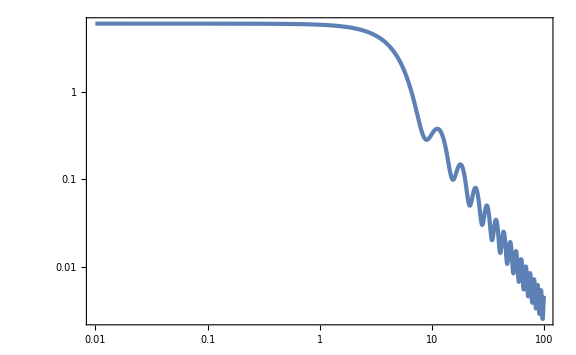

```mathematica
LogLogPlot[zetax[x,mu,0]/mu,{x,10^-2,10^2}]
```

```mathematica
CompactRTH[x_,mu_,kappa_]=2/3(1-(1+x D[zetax[x,mu,kappa], x])^2)//Simplify
```

2/3 (1-1/x^8(-384 mu+576 kappa^2 mu-72 mu x^2+96 kappa^2 mu x^2+x^4+24 mu (16-5 x^2+8 kappa^2 (-3+x^2)) Cos[x]+12 mu x (32-x^2+2 kappa^2 (-24+x^2)) Sin[x])^2)

```mathematica
Rx[x_,mu_,kappa_]=E^zetax[x,mu,kappa] x//Simplify
Rxp[x_,mu_,kappa_]=D[Rx[x,mu,kappa], x]//Simplify
deltax[x_,mu_,kappa_]=-8/9 E^(-5/2 zetax[x,mu,kappa])1/x^2 D[(x^2 D[E^(zetax[x,mu,kappa]/2), x]), x]//Simplify
```

ⅇ^(-(12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4) x

1/x^4 ⅇ^(-(12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4) (-384 mu+576 kappa^2 mu-72 mu x^2+96 kappa^2 mu x^2+x^4+24 mu (16-5 x^2+8 kappa^2 (-3+x^2)) Cos[x]+12 mu x (32-x^2+2 kappa^2 (-24+x^2)) Sin[x])

1/(3 x^10)16 ⅇ^((24 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4) mu (-9216 mu+27648 kappa^2 mu-20736 kappa^4 mu-3456 mu x^2+9792 kappa^2 mu x^2-6912 kappa^4 mu x^2-96 x^4+144 kappa^2 x^4-324 mu x^4+864 kappa^2 mu x^4-576 kappa^4 mu x^4-6 x^6+8 kappa^2 x^6-3 mu x^6+12 kappa^2 mu x^6-12 kappa^4 mu x^6+(x^4 (96-42 x^2+x^4-2 kappa^2 (72-32 x^2+x^4))-48 mu (-256+32 x^2+15 x^4+32 kappa^4 (-18+3 x^2+x^4)-4 kappa^2 (-192+28 x^2+11 x^4))) Cos[x]+3 mu (-1024+1664 x^2-164 x^4+x^6-4 kappa^2 (-768+1264 x^2-136 x^4+x^6)+4 kappa^4 (-576+960 x^2-112 x^4+x^6)) Cos[2 x]+12288 mu x Sin[x]-36864 kappa^2 mu x Sin[x]+27648 kappa^4 mu x Sin[x]+1920 mu x^3 Sin[x]-5184 kappa^2 mu x^3 Sin[x]+3456 kappa^4 mu x^3 Sin[x]+96 x^5 Sin[x]-144 kappa^2 x^5 Sin[x]-72 mu x^5 Sin[x]+240 kappa^2 mu x^5 Sin[x]-192 kappa^4 mu x^5 Sin[x]-10 x^7 Sin[x]+16 kappa^2 x^7 Sin[x]-6144 mu x Sin[2 x]+18432 kappa^2 mu x Sin[2 x]-13824 kappa^4 mu x Sin[2 x]+2112 mu x^3 Sin[2 x]-6624 kappa^2 mu x^3 Sin[2 x]+5184 kappa^4 mu x^3 Sin[2 x]-60 mu x^5 Sin[2 x]+216 kappa^2 mu x^5 Sin[2 x]-192 kappa^4 mu x^5 Sin[2 x])

```mathematica
CompactGintegrand[xp_,x_,mu_,kappa_]=4π deltax[xp,mu,kappa] Rx[xp,mu,kappa]^2 Rxp[xp,mu,kappa]Exp[(-Rx[xp,mu,kappa]^2)/(2 Rx[x,mu,kappa]^2)]/(2Sqrt[2] π^(3/2)Rx[x,mu,kappa])
```

1/(3 x xp^12)16 ⅇ^(-(ⅇ^((24 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4-(24 mu (-8+12 kappa^2-3 xp^2+4 kappa^2 xp^2+(8-xp^2+2 kappa^2 (-6+xp^2)) Cos[xp]-4 (-2+3 kappa^2) xp Sin[xp]))/xp^4) xp^2)/(2 x^2)+(12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4-(12 mu (-8+12 kappa^2-3 xp^2+4 kappa^2 xp^2+(8-xp^2+2 kappa^2 (-6+xp^2)) Cos[xp]-4 (-2+3 kappa^2) xp Sin[xp]))/xp^4) mu √(2/π) (-384 mu+576 kappa^2 mu-72 mu xp^2+96 kappa^2 mu xp^2+xp^4+24 mu (16-5 xp^2+8 kappa^2 (-3+xp^2)) Cos[xp]+12 mu xp (32-xp^2+2 kappa^2 (-24+xp^2)) Sin[xp]) (-9216 mu+27648 kappa^2 mu-20736 kappa^4 mu-3456 mu xp^2+9792 kappa^2 mu xp^2-6912 kappa^4 mu xp^2-96 xp^4+144 kappa^2 xp^4-324 mu xp^4+864 kappa^2 mu xp^4-576 kappa^4 mu xp^4-6 xp^6+8 kappa^2 xp^6-3 mu xp^6+12 kappa^2 mu xp^6-12 kappa^4 mu xp^6+(xp^4 (96-42 xp^2+xp^4-2 kappa^2 (72-32 xp^2+xp^4))-48 mu (-256+32 xp^2+15 xp^4+32 kappa^4 (-18+3 xp^2+xp^4)-4 kappa^2 (-192+28 xp^2+11 xp^4))) Cos[xp]+3 mu (-1024+1664 xp^2-164 xp^4+xp^6-4 kappa^2 (-768+1264 xp^2-136 xp^4+xp^6)+4 kappa^4 (-576+960 xp^2-112 xp^4+xp^6)) Cos[2 xp]+12288 mu xp Sin[xp]-36864 kappa^2 mu xp Sin[xp]+27648 kappa^4 mu xp Sin[xp]+1920 mu xp^3 Sin[xp]-5184 kappa^2 mu xp^3 Sin[xp]+3456 kappa^4 mu xp^3 Sin[xp]+96 xp^5 Sin[xp]-144 kappa^2 xp^5 Sin[xp]-72 mu xp^5 Sin[xp]+240 kappa^2 mu xp^5 Sin[xp]-192 kappa^4 mu xp^5 Sin[xp]-10 xp^7 Sin[xp]+16 kappa^2 xp^7 Sin[xp]-6144 mu xp Sin[2 xp]+18432 kappa^2 mu xp Sin[2 xp]-13824 kappa^4 mu xp Sin[2 xp]+2112 mu xp^3 Sin[2 xp]-6624 kappa^2 mu xp^3 Sin[2 xp]+5184 kappa^4 mu xp^3 Sin[2 xp]-60 mu xp^5 Sin[2 xp]+216 kappa^2 mu xp^5 Sin[2 xp]-192 kappa^4 mu xp^5 Sin[2 xp])

```mathematica
Normal[Series[CompactGintegrand[xp,x,mu,0],{x,∞,1},{xp,∞,1}]]
```

(16 mu √(2/π) Cos[xp]-(160 mu √(2/π) Sin[xp])/xp-(192 mu^2 √(2/π) Cos[xp] Sin[xp])/xp)/(3 x)

```mathematica
Integrate[Sin[xp]/xp,{xp,0,∞}]
```

π/2

```mathematica
Sin[xp]/xp/.{Sin[xp]->π/2 xp,Cos[xp]->1/2}
```

π/2

```mathematica
Integrate[Sin[xp]Cos[xp]/xp,{xp,0,∞}]
```

π/4

```mathematica
Sin[xp]Cos[xp]/xp/.{Sin[xp]->π/2 xp,Cos[xp]->1/2}
```

π/4

```mathematica
Normal[Series[CompactGintegrand[xp,x,mu,kappa],{x,∞,1},{xp,∞,1}]]
```

1/(3 x)(16 mu √(2/π) Cos[xp]-32 kappa^2 mu √(2/π) Cos[xp]-(160 mu √(2/π) Sin[xp])/xp+(256 kappa^2 mu √(2/π) Sin[xp])/xp-(192 mu^2 √(2/π) Cos[xp] Sin[xp])/xp+(768 kappa^2 mu^2 √(2/π) Cos[xp] Sin[xp])/xp-(768 kappa^4 mu^2 √(2/π) Cos[xp] Sin[xp])/xp)

```mathematica
Simplify[1/(3 x)(-(160 mu √(2/π) Sin[xp])/xp+(256 kappa^2 mu √(2/π) Sin[xp])/xp-(192 mu^2 √(2/π) Cos[xp] Sin[xp])/xp+(768 kappa^2 mu^2 √(2/π) Cos[xp] Sin[xp])/xp-(768 kappa^4 mu^2 √(2/π) Cos[xp] Sin[xp])/xp)]/.{Sin[xp]->π/2 xp,Cos[xp]->1/2}//Simplify
```

-(16 mu (5-8 kappa^2+3 (1-2 kappa^2)^2 mu) √(2 π))/(3 x)

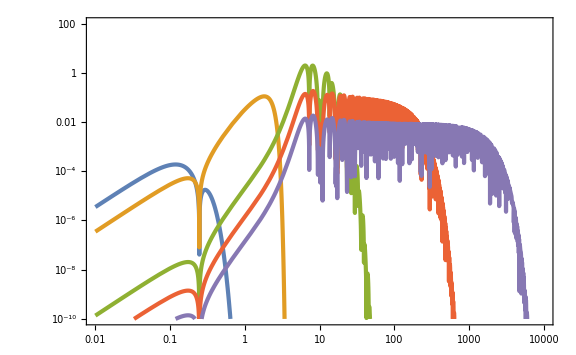

```mathematica
LogLogPlot[{Abs[CompactGintegrand[xp,10^-1,10^-2,10]],Abs[CompactGintegrand[xp,10^0,10^-2,10]],Abs[CompactGintegrand[xp,10^1,10^-2,10]],Abs[CompactGintegrand[xp,10^2,10^-2,10]],Abs[CompactGintegrand[xp,10^3,10^-2,10]]},{xp,10^-2,10^4},WorkingPrecision->30,PlotRange->{10^-10,10^2}]
```

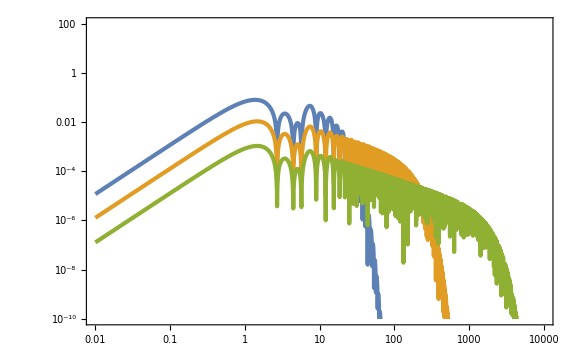

```mathematica
LogLogPlot[{Abs[CompactGintegrand[xp,10^1,6 10^-1,Sqrt[1/2]]],Abs[CompactGintegrand[xp,10^2,6 10^-1,Sqrt[1/2]]],Abs[CompactGintegrand[xp,10^3,6 10^-1,Sqrt[1/2]]]},{xp,10^-2,10^4},WorkingPrecision->30,PlotRange->{10^-10,10^2}]
```

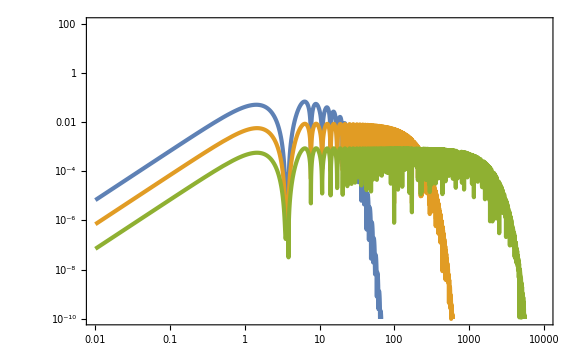

```mathematica
LogLogPlot[{Abs[CompactGintegrand[xp,10^1,6 10^-1,Sqrt[2/3]]],Abs[CompactGintegrand[xp,10^2,6 10^-1,Sqrt[2/3]]],Abs[CompactGintegrand[xp,10^3,6 10^-1,Sqrt[2/3]]]},{xp,10^-2,10^4},WorkingPrecision->30,PlotRange->{10^-10,10^2}]
```

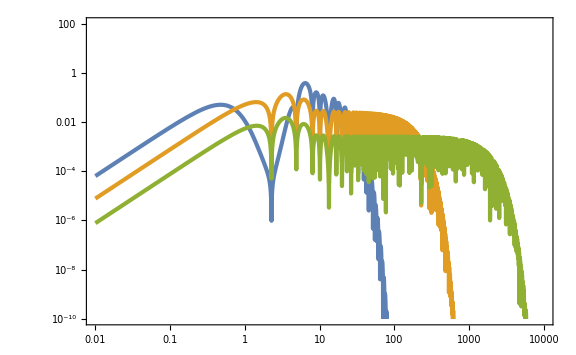

```mathematica
LogLogPlot[{Abs[CompactGintegrand[xp,10^1,6 10^-1,0]],Abs[CompactGintegrand[xp,10^2,6 10^-1,0]],Abs[CompactGintegrand[xp,10^3,6 10^-1,0]]},{xp,10^-2,10^4},WorkingPrecision->30,PlotRange->{10^-10,10^2}]
```

```mathematica
Sqrt[2/3]//N
```

0.816497

```mathematica
CompactG[x_,mu_,kappa_]:=4π NIntegrate[deltax[xp,mu,kappa] Rx[xp,mu,kappa]^2 Rxp[xp,mu,kappa]Exp[(-Rx[xp,mu,kappa]^2)/(2 Rx[x,mu,kappa]^2)],{xp,0,10^2},WorkingPrecision->30,MaxRecursion->20]/(2Sqrt[2] π^(3/2)Rx[x,mu,kappa])
```

```mathematica
CompactGList=ParallelTable[{10^logx,CompactG[10^logx,6 10^-1,Sqrt[1/2]]},{logx,-2,4,10^-1}];//AbsoluteTiming
```

{19.823,Null}

```mathematica
<<init`
```

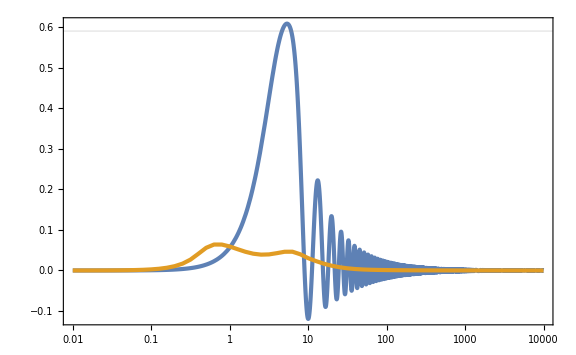

```mathematica
Show[LogLinearPlot[CompactRTH[x,0.13,10^-4],{x,10^-2,10^4},GridLines->{None,{0.59}},PlotRange->Full],ListLogLinearPlot[CompactGList,PlotStyle->{Color[2],AbsoluteThickness[3]}]]
```

### zeta

```mathematica
$Assumptions={n>0,As>0,kUV>0,kIR>0,kUV>kIR,mu0>0,kappa>0,Nw>0};
```

```mathematica
sigman[n_,kUV_,kIR_,As_]=Sqrt[As Integrate[Exp[2n logk],{logk,Log[kIR],Log[kUV]}]]//Simplify
```

(√((As (-kIR^(2 n)+kUV^(2 n)))/n))/(√2)

```mathematica
sigman[0,kUV_,kIR_,As_]=Sqrt[As Integrate[1,{logk,Log[kIR],Log[kUV]}]]//Simplify
```

√(As Log[kUV/kIR])

```mathematica
psin[n_,r_,kUV_,kIR_]=1/sigman[n,kUV,kIR,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,kIR,kUV}]//Simplify
```

(n (r^2)^(-2 n) ((ⅈ r)^(2 n) (-Gamma[-1+2 n,-ⅈ kIR r]+Gamma[-1+2 n,-ⅈ kUV r])+(-ⅈ r)^(2 n) (-Gamma[-1+2 n,ⅈ kIR r]+Gamma[-1+2 n,ⅈ kUV r])))/(-kIR^(2 n)+kUV^(2 n))

```mathematica
psin[0_,r_,kUV_,kIR_]=1/sigman[0,kUV,kIR,As]^2 As Integrate[Sin[k r]/(k r)1/k,{k,kIR,kUV}]//Simplify
```

(-r CosIntegral[kIR r]+r CosIntegral[kUV r]+Sin[kIR r]/kIR-Sin[kUV r]/kUV)/(r Log[kUV/kIR])

```mathematica
psin[1,r,kUV,kIR]//ExpToTrig//Simplify
psin[2,r,kUV,kIR]//ExpToTrig//Simplify
```

-(2 (Cos[kIR r]-Cos[kUV r]))/((kIR^2-kUV^2) r^2)

(2 (Gamma[3,-ⅈ kIR r]+Gamma[3,ⅈ kIR r]-Gamma[3,-ⅈ kUV r]-Gamma[3,ⅈ kUV r]))/((kIR^4-kUV^4) r^4)

```mathematica
Lappsin[n_,r_,kUV_,kIR_]=(-sigman[n+1,kUV,kIR,As]^2)/sigman[n,kUV,kIR,As]^2 psin[n+1,r,kUV,kIR]//Simplify
```

-(n (r^2)^(-2 (1+n)) ((ⅈ r)^(2 (1+n)) (-Gamma[1+2 n,-ⅈ kIR r]+Gamma[1+2 n,-ⅈ kUV r])+(-ⅈ r)^(2 (1+n)) (-Gamma[1+2 n,ⅈ kIR r]+Gamma[1+2 n,ⅈ kUV r])))/(-kIR^(2 n)+kUV^(2 n))

```mathematica
Lappsin[0,r_,kUV_,kIR_]=(-sigman[1,kUV,kIR,As]^2)/sigman[0,kUV,kIR,As]^2 psin[1,r,kUV,kIR]//ExpToTrig//Simplify
```

(-Cos[kIR r]+Cos[kUV r])/(r^2 Log[kUV/kIR])

```mathematica
gamman[n_,kUV_,kIR_]=sigman[n,kUV,kIR,As]^2/(sigman[n-1,kUV,kIR,As]sigman[n+1,kUV,kIR,As])//Simplify
Rn[n_,kUV_,kIR_]=√3 sigman[n,kUV,kIR,As]/sigman[n+1,kUV,kIR,As]//Simplify
```

(-kIR^(2 n)+kUV^(2 n))/(√(-kIR^(2+2 n)+kUV^(2+2 n)) n √((-kIR^(-2+2 n)+kUV^(-2+2 n))/(-1+n^2)))

(√3 √((-kIR^(2 n)+kUV^(2 n)) (1+n)))/(√((-kIR^(2+2 n)+kUV^(2+2 n)) n))

```mathematica
gamman[1,kUV_,kIR_]=sigman[1,kUV,kIR,As]^2/(sigman[0,kUV,kIR,As]sigman[2,kUV,kIR,As])//Simplify
```

(-kIR^2+kUV^2)/(√((-kIR^4+kUV^4) Log[kUV/kIR]))

```mathematica
ghat[r_,kUV_,kIR_,mu0_,k1_]=mu0(1/(1-gamman[1,kUV,kIR]^2)(psin[0,r,kUV,kIR]+1/3 Rn[1,kUV,kIR]^2 Lappsin[0,r,kUV,kIR])-k1^2 1/(gamman[1,kUV,kIR](1-gamman[1,kUV,kIR]^2))sigman[0,kUV,kIR,As]/sigman[2,kUV,kIR,As](gamman[1,kUV,kIR]^2 psin[0,r,kUV,kIR]+1/3 Rn[1,kUV,kIR]^2 Lappsin[0,r,kUV,kIR]))//Simplify
```

((kIR^2+kUV^2) mu0 (-(2 (Cos[kIR r]-Cos[kUV r]))/(kIR^2+kUV^2)+r (-r CosIntegral[kIR r]+r CosIntegral[kUV r]+Sin[kIR r]/kIR-Sin[kUV r]/kUV)+1/(kIR kUV (kIR^4-kUV^4))2 k1^2 (kIR kUV (kIR^2-kUV^2) r^2 CosIntegral[kIR r]+kIR kUV (-kIR^2+kUV^2) r^2 CosIntegral[kUV r]-2 kIR kUV Cos[kIR r] Log[kUV/kIR]+2 kIR kUV Cos[kUV r] Log[kUV/kIR]-kIR^2 kUV r Sin[kIR r]+kUV^3 r Sin[kIR r]+kIR^3 r Sin[kUV r]-kIR kUV^2 r Sin[kUV r])))/(r^2 (kIR^2-kUV^2+(kIR^2+kUV^2) Log[kUV/kIR]))

```mathematica
sigman[0,kUV,kIR,As]/sigman[2,kUV,kIR,As]//Simplify
```

2 √(Log[kUV/kIR]/(-kIR^4+kUV^4))

```mathematica
gx[x_,Nw_,mu_,kappa_]=ghat[x/kIR,E^Nw kIR,kIR,mu,kappa/Sqrt[sigman[0,E^Nw kIR,kIR,As]/sigman[2,E^Nw kIR,kIR,As]]]//Simplify
```

1/((1+ⅇ^(2 Nw) (-1+Nw)+Nw) x^2)(1+ⅇ^(2 Nw)) mu (-(2 (Cos[x]-Cos[ⅇ^Nw x]))/(1+ⅇ^(2 Nw))+x (-x CosIntegral[x]+x CosIntegral[ⅇ^Nw x]+Sin[x]-ⅇ^-Nw Sin[ⅇ^Nw x])+1/(√((-1+ⅇ^(4 Nw)) Nw))ⅇ^-Nw kappa^2 (2 ⅇ^Nw Nw Cos[x]-2 ⅇ^Nw Nw Cos[ⅇ^Nw x]+ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[x]-ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[ⅇ^Nw x]+ⅇ^Nw x Sin[x]-ⅇ^(3 Nw) x Sin[x]-x Sin[ⅇ^Nw x]+ⅇ^(2 Nw) x Sin[ⅇ^Nw x]))

```mathematica
1/Sqrt[sigman[0,E^Nw kIR,kIR,As]/sigman[2,E^Nw kIR,kIR,As]]/kIR/.{Nw->5}//Simplify//N
```

70.1802

```mathematica
E^5//N
```

148.413

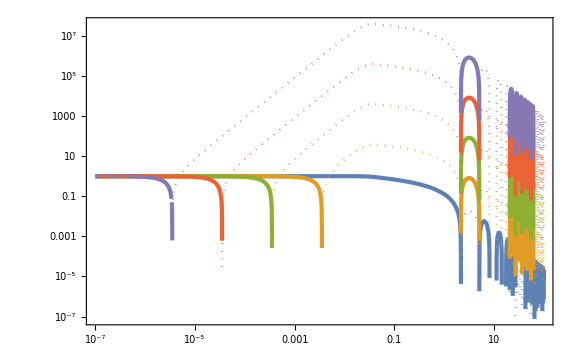

```mathematica
LogLogPlot[{gx[x,5,1,0],-gx[x,5,1,0],gx[x,5,1,10^1],-gx[x,5,1,10^1],gx[x,5,1,10^2],-gx[x,5,1,10^2],gx[x,5,1,10^3],-gx[x,5,1,10^3],gx[x,5,1,10^4],-gx[x,5,1,10^4]},{x,10^-7,10^2},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],AbsoluteThickness[3]},{Color[2],Dotted},{Color[3],AbsoluteThickness[3]},{Color[3],Dotted},{Color[4],AbsoluteThickness[3]},{Color[4],Dotted},{Color[5],AbsoluteThickness[3]},{Color[5],Dotted}},WorkingPrecision->30]
```

```mathematica
CompactRTH[x_,Nw_,mu_,kappa_]=2/3(1-(1+x D[gx[x,Nw,mu,kappa], x])^2)//Simplify
```

2/3 (1-(ⅇ^(-2 Nw) (-4 ⅇ^Nw mu ((1+ⅇ^(2 Nw)) kappa^2 Nw-√((-1+ⅇ^(4 Nw)) Nw)) Cos[x]+4 ⅇ^Nw mu ((1+ⅇ^(2 Nw)) kappa^2 Nw-√((-1+ⅇ^(4 Nw)) Nw)) Cos[ⅇ^Nw x]+x (ⅇ^Nw √((-1+ⅇ^(4 Nw)) Nw) (1+ⅇ^(2 Nw) (-1+Nw)+Nw) x+ⅇ^Nw mu ((1+ⅇ^(2 Nw)) kappa^2 (-1+ⅇ^(2 Nw)-2 Nw)-(-1+ⅇ^(2 Nw)) √((-1+ⅇ^(4 Nw)) Nw)) Sin[x]-mu ((-1+ⅇ^(2 Nw)) √((-1+ⅇ^(4 Nw)) Nw)+kappa^2 (-1+ⅇ^(4 Nw) (1-2 Nw)-2 ⅇ^(2 Nw) Nw)) Sin[ⅇ^Nw x]))^2)/((-1+ⅇ^(4 Nw)) Nw (1+ⅇ^(2 Nw) (-1+Nw)+Nw)^2 x^4))

```mathematica
Rx[x_,Nw_,mu_,kappa_]=E^gx[x,Nw,mu,kappa] x//Simplify
Rxp[x_,Nw_,mu_,kappa_]=D[Rx[x,Nw,mu,kappa], x]//Simplify
deltax[x_,Nw_,mu_,kappa_]=-8/9 E^(-5/2 gx[x,Nw,mu,kappa])1/x^2 D[(x^2 D[E^(gx[x,Nw,mu,kappa]/2), x]), x]//Simplify
```

ⅇ^(((1+ⅇ^(2 Nw)) mu (-(2 (Cos[x]-Cos[ⅇ^Nw x]))/(1+ⅇ^(2 Nw))+x (-x CosIntegral[x]+x CosIntegral[ⅇ^Nw x]+Sin[x]-ⅇ^-Nw Sin[ⅇ^Nw x])+(ⅇ^-Nw kappa^2 (2 ⅇ^Nw Nw Cos[x]-2 ⅇ^Nw Nw Cos[ⅇ^Nw x]+ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[x]-ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[ⅇ^Nw x]+ⅇ^Nw x Sin[x]-ⅇ^(3 Nw) x Sin[x]-x Sin[ⅇ^Nw x]+ⅇ^(2 Nw) x Sin[ⅇ^Nw x]))/(√((-1+ⅇ^(4 Nw)) Nw))))/((1+ⅇ^(2 Nw) (-1+Nw)+Nw) x^2)) x

(ⅇ^(-Nw+((1+ⅇ^(2 Nw)) mu (-(2 (Cos[x]-Cos[ⅇ^Nw x]))/(1+ⅇ^(2 Nw))+x (-x CosIntegral[x]+x CosIntegral[ⅇ^Nw x]+Sin[x]-ⅇ^-Nw Sin[ⅇ^Nw x])+(ⅇ^-Nw kappa^2 (2 ⅇ^Nw Nw Cos[x]-2 ⅇ^Nw Nw Cos[ⅇ^Nw x]+ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[x]-ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[ⅇ^Nw x]+ⅇ^Nw x Sin[x]-ⅇ^(3 Nw) x Sin[x]-x Sin[ⅇ^Nw x]+ⅇ^(2 Nw) x Sin[ⅇ^Nw x]))/(√((-1+ⅇ^(4 Nw)) Nw))))/((1+ⅇ^(2 Nw) (-1+Nw)+Nw) x^2)) (-4 ⅇ^Nw mu ((1+ⅇ^(2 Nw)) kappa^2 Nw-√((-1+ⅇ^(4 Nw)) Nw)) Cos[x]+4 ⅇ^Nw mu ((1+ⅇ^(2 Nw)) kappa^2 Nw-√((-1+ⅇ^(4 Nw)) Nw)) Cos[ⅇ^Nw x]+x (ⅇ^Nw √((-1+ⅇ^(4 Nw)) Nw) (1+ⅇ^(2 Nw) (-1+Nw)+Nw) x+ⅇ^Nw mu ((1+ⅇ^(2 Nw)) kappa^2 (-1+ⅇ^(2 Nw)-2 Nw)-(-1+ⅇ^(2 Nw)) √((-1+ⅇ^(4 Nw)) Nw)) Sin[x]-mu ((-1+ⅇ^(2 Nw)) √((-1+ⅇ^(4 Nw)) Nw)+kappa^2 (-1+ⅇ^(4 Nw) (1-2 Nw)-2 ⅇ^(2 Nw) Nw)) Sin[ⅇ^Nw x])))/(√((-1+ⅇ^(4 Nw)) Nw) (1+ⅇ^(2 Nw) (-1+Nw)+Nw) x^2)

-((2 ⅇ^(-2 (Nw+((1+ⅇ^(2 Nw)) mu (-(2 (Cos[x]-Cos[ⅇ^Nw x]))/(1+ⅇ^(2 Nw))+x (-x CosIntegral[x]+x CosIntegral[ⅇ^Nw x]+Sin[x]-ⅇ^-Nw Sin[ⅇ^Nw x])+(ⅇ^-Nw kappa^2 (2 ⅇ^Nw Nw Cos[x]-2 ⅇ^Nw Nw Cos[ⅇ^Nw x]+ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[x]-ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[ⅇ^Nw x]+ⅇ^Nw x Sin[x]-ⅇ^(3 Nw) x Sin[x]-x Sin[ⅇ^Nw x]+ⅇ^(2 Nw) x Sin[ⅇ^Nw x]))/(√((-1+ⅇ^(4 Nw)) Nw))))/((1+ⅇ^(2 Nw) (-1+Nw)+Nw) x^2))) mu (16 ⅇ^(2 Nw) mu Nw (-1+kappa^4 Nw-2 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+ⅇ^(2 Nw) (1+kappa^4 Nw)) Cos[x]^2+16 ⅇ^(2 Nw) mu Nw (-1+kappa^4 Nw-2 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+ⅇ^(2 Nw) (1+kappa^4 Nw)) Cos[ⅇ^Nw x]^2-2 ⅇ^(2 Nw) x Cos[ⅇ^Nw x] (x ((-1+ⅇ^(4 Nw)) Nw^2 (-4+(-1+ⅇ^(2 Nw)) x^2)-(-1+ⅇ^(2 Nw)) Nw (4+x^2+ⅇ^(4 Nw) x^2-kappa^2 √((-1+ⅇ^(4 Nw)) Nw) (-4+x^2)-ⅇ^(2 Nw) (4+(2+3 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)) x^2))-kappa^2 (-4 √((-1+ⅇ^(4 Nw)) Nw^5)+√((-1+ⅇ^(4 Nw)) Nw) x^2+ⅇ^(4 Nw) (√((-1+ⅇ^(4 Nw)) Nw)+2 √((-1+ⅇ^(4 Nw)) Nw^5)) x^2+2 ⅇ^(2 Nw) (-2 √((-1+ⅇ^(4 Nw)) Nw^5)-(√((-1+ⅇ^(4 Nw)) Nw)-√((-1+ⅇ^(4 Nw)) Nw^5)) x^2)))+4 mu (2 (1+ⅇ^(2 Nw)) kappa^4 Nw^2+(-1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw)-Nw (1-kappa^4+ⅇ^(4 Nw) (1+kappa^4)+3 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)-ⅇ^(2 Nw) (2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)))) Sin[x])-2 ⅇ^Nw Cos[x] (16 ⅇ^Nw mu Nw (-1+kappa^4 Nw-2 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+ⅇ^(2 Nw) (1+kappa^4 Nw)) Cos[ⅇ^Nw x]+x (ⅇ^Nw x ((-1+ⅇ^(4 Nw)) Nw^2 (4+(-1+ⅇ^(2 Nw)) x^2)-(-1+ⅇ^(2 Nw)) Nw (-4+x^2+ⅇ^(4 Nw) x^2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw) (-4+3 x^2)+ⅇ^(2 Nw) (4+(-2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)) x^2))+kappa^2 (-4 √((-1+ⅇ^(4 Nw)) Nw^5)+ⅇ^(4 Nw) √((-1+ⅇ^(4 Nw)) Nw) x^2+(√((-1+ⅇ^(4 Nw)) Nw)+2 √((-1+ⅇ^(4 Nw)) Nw^5)) x^2+2 ⅇ^(2 Nw) (-2 √((-1+ⅇ^(4 Nw)) Nw^5)-(√((-1+ⅇ^(4 Nw)) Nw)-√((-1+ⅇ^(4 Nw)) Nw^5)) x^2)))+4 ⅇ^Nw (1-kappa^4+ⅇ^(4 Nw) (1+kappa^4)) mu Nw Sin[x]+4 mu (2 ⅇ^(2 Nw) (1+ⅇ^(2 Nw)) kappa^4 Nw^2+(-1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+Nw (1+kappa^4-ⅇ^(4 Nw) (-1+kappa^4)+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)-ⅇ^(2 Nw) (2+3 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)))) Sin[ⅇ^Nw x]))+x (ⅇ^(2 Nw) mu ((1+ⅇ^(2 Nw)) kappa^4 (-1+ⅇ^(2 Nw)-2 Nw)^2+(-1+ⅇ^(2 Nw))^3 Nw-2 (-1+ⅇ^(2 Nw)) kappa^2 (-1+ⅇ^(2 Nw)-2 Nw) √((-1+ⅇ^(4 Nw)) Nw)) x Sin[x]^2+4 ⅇ^(2 Nw) mu (2 kappa^4 Nw^2-kappa^2 √((-1+ⅇ^(4 Nw)) Nw) (1+3 Nw)+ⅇ^(2 Nw) (2 kappa^4 Nw^2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+Nw (2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)))) Sin[2 x]+2 ⅇ^Nw x Sin[x] (-4 ⅇ^Nw ((-1+ⅇ^(4 Nw)) Nw^2-(1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw^5)-(-1+ⅇ^(2 Nw)) Nw (-1+ⅇ^(2 Nw)-kappa^2 √((-1+ⅇ^(4 Nw)) Nw))) x+mu ((-1+ⅇ^(2 Nw))^3 Nw-2 (-1+ⅇ^(2 Nw))^2 kappa^2 Nw √((-1+ⅇ^(4 Nw)) Nw)+(1+ⅇ^(2 Nw)) kappa^4 (-1-2 Nw+ⅇ^(4 Nw) (-1+2 Nw)+ⅇ^(2 Nw) (2-4 Nw^2))) Sin[ⅇ^Nw x])+Sin[ⅇ^Nw x] (8 ⅇ^Nw mu (2 ⅇ^(2 Nw) (1+ⅇ^(2 Nw)) kappa^4 Nw^2+(-1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+Nw (1+kappa^4-ⅇ^(4 Nw) (-1+kappa^4)+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)-ⅇ^(2 Nw) (2+3 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)))) Cos[ⅇ^Nw x]+x (8 ⅇ^(3 Nw) ((-1+ⅇ^(4 Nw)) Nw^2-(1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw^5)-(-1+ⅇ^(2 Nw)) Nw (-1+ⅇ^(2 Nw)-kappa^2 √((-1+ⅇ^(4 Nw)) Nw))) x+mu ((1+ⅇ^(2 Nw)) kappa^4 (-1+ⅇ^(2 Nw) (1-2 Nw))^2+(-1+ⅇ^(2 Nw))^3 Nw+2 (-1+ⅇ^(2 Nw)) kappa^2 (-√((-1+ⅇ^(4 Nw)) Nw)+ⅇ^(2 Nw) (√((-1+ⅇ^(4 Nw)) Nw)-2 √((-1+ⅇ^(4 Nw)) Nw^3)))) Sin[ⅇ^Nw x])))))/(9 (-1+ⅇ^(2 Nw)) Nw (1+ⅇ^(2 Nw) (-1+Nw)+Nw)^2 x^6))

```mathematica
CompactGintegrand[xp_,x_,Nw_,mu_,kappa_]=4π deltax[xp,Nw,mu,kappa] Rx[xp,Nw,mu,kappa]^2 Rxp[xp,Nw,mu,kappa]Exp[(-Rx[xp,Nw,mu,kappa]^2)/(2 Rx[x,Nw,mu,kappa]^2)]/(2Sqrt[2] π^(3/2)Rx[x,Nw,mu,kappa])
```

-((2 ⅇ^(-Nw-(ⅇ^(-(2 (1+ⅇ^(2 Nw)) mu (-(2 (Cos[x]-Cos[ⅇ^Nw x]))/(1+ⅇ^(2 Nw))+x (-x CosIntegral[x]+x CosIntegral[ⅇ^Nw x]+Sin[x]-ⅇ^-Nw Sin[ⅇ^Nw x])+(ⅇ^-Nw kappa^2 (2 ⅇ^Nw Nw Cos[x]-2 ⅇ^Nw Nw Cos[ⅇ^Nw x]+ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[x]-ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[ⅇ^Nw x]+ⅇ^Nw x Sin[x]-ⅇ^(3 Nw) x Sin[x]-x Sin[ⅇ^Nw x]+ⅇ^(2 Nw) x Sin[ⅇ^Nw x]))/(√((-1+ⅇ^(4 Nw)) Nw))))/((1+ⅇ^(2 Nw) (-1+Nw)+Nw) x^2)+(2 (1+ⅇ^(2 Nw)) mu (-(2 (Cos[xp]-Cos[ⅇ^Nw xp]))/(1+ⅇ^(2 Nw))+xp (-xp CosIntegral[xp]+xp CosIntegral[ⅇ^Nw xp]+Sin[xp]-ⅇ^-Nw Sin[ⅇ^Nw xp])+(ⅇ^-Nw kappa^2 (2 ⅇ^Nw Nw Cos[xp]-2 ⅇ^Nw Nw Cos[ⅇ^Nw xp]+ⅇ^Nw (-1+ⅇ^(2 Nw)) xp^2 CosIntegral[xp]-ⅇ^Nw (-1+ⅇ^(2 Nw)) xp^2 CosIntegral[ⅇ^Nw xp]+ⅇ^Nw xp Sin[xp]-ⅇ^(3 Nw) xp Sin[xp]-xp Sin[ⅇ^Nw xp]+ⅇ^(2 Nw) xp Sin[ⅇ^Nw xp]))/(√((-1+ⅇ^(4 Nw)) Nw))))/((1+ⅇ^(2 Nw) (-1+Nw)+Nw) xp^2)) xp^2)/(2 x^2)-((1+ⅇ^(2 Nw)) mu (-(2 (Cos[x]-Cos[ⅇ^Nw x]))/(1+ⅇ^(2 Nw))+x (-x CosIntegral[x]+x CosIntegral[ⅇ^Nw x]+Sin[x]-ⅇ^-Nw Sin[ⅇ^Nw x])+(ⅇ^-Nw kappa^2 (2 ⅇ^Nw Nw Cos[x]-2 ⅇ^Nw Nw Cos[ⅇ^Nw x]+ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[x]-ⅇ^Nw (-1+ⅇ^(2 Nw)) x^2 CosIntegral[ⅇ^Nw x]+ⅇ^Nw x Sin[x]-ⅇ^(3 Nw) x Sin[x]-x Sin[ⅇ^Nw x]+ⅇ^(2 Nw) x Sin[ⅇ^Nw x]))/(√((-1+ⅇ^(4 Nw)) Nw))))/((1+ⅇ^(2 Nw) (-1+Nw)+Nw) x^2)+(3 (1+ⅇ^(2 Nw)) mu (-(2 (Cos[xp]-Cos[ⅇ^Nw xp]))/(1+ⅇ^(2 Nw))+xp (-xp CosIntegral[xp]+xp CosIntegral[ⅇ^Nw xp]+Sin[xp]-ⅇ^-Nw Sin[ⅇ^Nw xp])+(ⅇ^-Nw kappa^2 (2 ⅇ^Nw Nw Cos[xp]-2 ⅇ^Nw Nw Cos[ⅇ^Nw xp]+ⅇ^Nw (-1+ⅇ^(2 Nw)) xp^2 CosIntegral[xp]-ⅇ^Nw (-1+ⅇ^(2 Nw)) xp^2 CosIntegral[ⅇ^Nw xp]+ⅇ^Nw xp Sin[xp]-ⅇ^(3 Nw) xp Sin[xp]-xp Sin[ⅇ^Nw xp]+ⅇ^(2 Nw) xp Sin[ⅇ^Nw xp]))/(√((-1+ⅇ^(4 Nw)) Nw))))/((1+ⅇ^(2 Nw) (-1+Nw)+Nw) xp^2)-2 (Nw+((1+ⅇ^(2 Nw)) mu (-(2 (Cos[xp]-Cos[ⅇ^Nw xp]))/(1+ⅇ^(2 Nw))+xp (-xp CosIntegral[xp]+xp CosIntegral[ⅇ^Nw xp]+Sin[xp]-ⅇ^-Nw Sin[ⅇ^Nw xp])+(ⅇ^-Nw kappa^2 (2 ⅇ^Nw Nw Cos[xp]-2 ⅇ^Nw Nw Cos[ⅇ^Nw xp]+ⅇ^Nw (-1+ⅇ^(2 Nw)) xp^2 CosIntegral[xp]-ⅇ^Nw (-1+ⅇ^(2 Nw)) xp^2 CosIntegral[ⅇ^Nw xp]+ⅇ^Nw xp Sin[xp]-ⅇ^(3 Nw) xp Sin[xp]-xp Sin[ⅇ^Nw xp]+ⅇ^(2 Nw) xp Sin[ⅇ^Nw xp]))/(√((-1+ⅇ^(4 Nw)) Nw))))/((1+ⅇ^(2 Nw) (-1+Nw)+Nw) xp^2))) mu √(2/π) (-4 ⅇ^Nw mu ((1+ⅇ^(2 Nw)) kappa^2 Nw-√((-1+ⅇ^(4 Nw)) Nw)) Cos[xp]+4 ⅇ^Nw mu ((1+ⅇ^(2 Nw)) kappa^2 Nw-√((-1+ⅇ^(4 Nw)) Nw)) Cos[ⅇ^Nw xp]+xp (ⅇ^Nw √((-1+ⅇ^(4 Nw)) Nw) (1+ⅇ^(2 Nw) (-1+Nw)+Nw) xp+ⅇ^Nw mu ((1+ⅇ^(2 Nw)) kappa^2 (-1+ⅇ^(2 Nw)-2 Nw)-(-1+ⅇ^(2 Nw)) √((-1+ⅇ^(4 Nw)) Nw)) Sin[xp]-mu ((-1+ⅇ^(2 Nw)) √((-1+ⅇ^(4 Nw)) Nw)+kappa^2 (-1+ⅇ^(4 Nw) (1-2 Nw)-2 ⅇ^(2 Nw) Nw)) Sin[ⅇ^Nw xp])) (16 ⅇ^(2 Nw) mu Nw (-1+kappa^4 Nw-2 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+ⅇ^(2 Nw) (1+kappa^4 Nw)) Cos[xp]^2+16 ⅇ^(2 Nw) mu Nw (-1+kappa^4 Nw-2 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+ⅇ^(2 Nw) (1+kappa^4 Nw)) Cos[ⅇ^Nw xp]^2-2 ⅇ^(2 Nw) xp Cos[ⅇ^Nw xp] (xp ((-1+ⅇ^(4 Nw)) Nw^2 (-4+(-1+ⅇ^(2 Nw)) xp^2)-(-1+ⅇ^(2 Nw)) Nw (4+xp^2+ⅇ^(4 Nw) xp^2-kappa^2 √((-1+ⅇ^(4 Nw)) Nw) (-4+xp^2)-ⅇ^(2 Nw) (4+(2+3 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)) xp^2))-kappa^2 (-4 √((-1+ⅇ^(4 Nw)) Nw^5)+√((-1+ⅇ^(4 Nw)) Nw) xp^2+ⅇ^(4 Nw) (√((-1+ⅇ^(4 Nw)) Nw)+2 √((-1+ⅇ^(4 Nw)) Nw^5)) xp^2+2 ⅇ^(2 Nw) (-2 √((-1+ⅇ^(4 Nw)) Nw^5)-(√((-1+ⅇ^(4 Nw)) Nw)-√((-1+ⅇ^(4 Nw)) Nw^5)) xp^2)))+4 mu (2 (1+ⅇ^(2 Nw)) kappa^4 Nw^2+(-1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw)-Nw (1-kappa^4+ⅇ^(4 Nw) (1+kappa^4)+3 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)-ⅇ^(2 Nw) (2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)))) Sin[xp])-2 ⅇ^Nw Cos[xp] (16 ⅇ^Nw mu Nw (-1+kappa^4 Nw-2 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+ⅇ^(2 Nw) (1+kappa^4 Nw)) Cos[ⅇ^Nw xp]+xp (ⅇ^Nw xp ((-1+ⅇ^(4 Nw)) Nw^2 (4+(-1+ⅇ^(2 Nw)) xp^2)-(-1+ⅇ^(2 Nw)) Nw (-4+xp^2+ⅇ^(4 Nw) xp^2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw) (-4+3 xp^2)+ⅇ^(2 Nw) (4+(-2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)) xp^2))+kappa^2 (-4 √((-1+ⅇ^(4 Nw)) Nw^5)+ⅇ^(4 Nw) √((-1+ⅇ^(4 Nw)) Nw) xp^2+(√((-1+ⅇ^(4 Nw)) Nw)+2 √((-1+ⅇ^(4 Nw)) Nw^5)) xp^2+2 ⅇ^(2 Nw) (-2 √((-1+ⅇ^(4 Nw)) Nw^5)-(√((-1+ⅇ^(4 Nw)) Nw)-√((-1+ⅇ^(4 Nw)) Nw^5)) xp^2)))+4 ⅇ^Nw (1-kappa^4+ⅇ^(4 Nw) (1+kappa^4)) mu Nw Sin[xp]+4 mu (2 ⅇ^(2 Nw) (1+ⅇ^(2 Nw)) kappa^4 Nw^2+(-1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+Nw (1+kappa^4-ⅇ^(4 Nw) (-1+kappa^4)+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)-ⅇ^(2 Nw) (2+3 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)))) Sin[ⅇ^Nw xp]))+xp (ⅇ^(2 Nw) mu ((1+ⅇ^(2 Nw)) kappa^4 (-1+ⅇ^(2 Nw)-2 Nw)^2+(-1+ⅇ^(2 Nw))^3 Nw-2 (-1+ⅇ^(2 Nw)) kappa^2 (-1+ⅇ^(2 Nw)-2 Nw) √((-1+ⅇ^(4 Nw)) Nw)) xp Sin[xp]^2+4 ⅇ^(2 Nw) mu (2 kappa^4 Nw^2-kappa^2 √((-1+ⅇ^(4 Nw)) Nw) (1+3 Nw)+ⅇ^(2 Nw) (2 kappa^4 Nw^2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+Nw (2+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)))) Sin[2 xp]+2 ⅇ^Nw xp Sin[xp] (-4 ⅇ^Nw ((-1+ⅇ^(4 Nw)) Nw^2-(1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw^5)-(-1+ⅇ^(2 Nw)) Nw (-1+ⅇ^(2 Nw)-kappa^2 √((-1+ⅇ^(4 Nw)) Nw))) xp+mu ((-1+ⅇ^(2 Nw))^3 Nw-2 (-1+ⅇ^(2 Nw))^2 kappa^2 Nw √((-1+ⅇ^(4 Nw)) Nw)+(1+ⅇ^(2 Nw)) kappa^4 (-1-2 Nw+ⅇ^(4 Nw) (-1+2 Nw)+ⅇ^(2 Nw) (2-4 Nw^2))) Sin[ⅇ^Nw xp])+Sin[ⅇ^Nw xp] (8 ⅇ^Nw mu (2 ⅇ^(2 Nw) (1+ⅇ^(2 Nw)) kappa^4 Nw^2+(-1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw)+Nw (1+kappa^4-ⅇ^(4 Nw) (-1+kappa^4)+kappa^2 √((-1+ⅇ^(4 Nw)) Nw)-ⅇ^(2 Nw) (2+3 kappa^2 √((-1+ⅇ^(4 Nw)) Nw)))) Cos[ⅇ^Nw xp]+xp (8 ⅇ^(3 Nw) ((-1+ⅇ^(4 Nw)) Nw^2-(1+ⅇ^(2 Nw)) kappa^2 √((-1+ⅇ^(4 Nw)) Nw^5)-(-1+ⅇ^(2 Nw)) Nw (-1+ⅇ^(2 Nw)-kappa^2 √((-1+ⅇ^(4 Nw)) Nw))) xp+mu ((1+ⅇ^(2 Nw)) kappa^4 (-1+ⅇ^(2 Nw) (1-2 Nw))^2+(-1+ⅇ^(2 Nw))^3 Nw+2 (-1+ⅇ^(2 Nw)) kappa^2 (-√((-1+ⅇ^(4 Nw)) Nw)+ⅇ^(2 Nw) (√((-1+ⅇ^(4 Nw)) Nw)-2 √((-1+ⅇ^(4 Nw)) Nw^3)))) Sin[ⅇ^Nw xp])))))/(9 (-1+ⅇ^(2 Nw)) Nw √((-1+ⅇ^(4 Nw)) Nw) (1+ⅇ^(2 Nw) (-1+Nw)+Nw)^3 x xp^6))

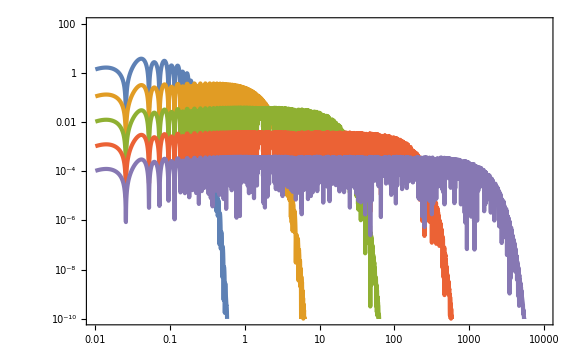

```mathematica
LogLogPlot[{Abs[CompactGintegrand[xp,10^-1,5,10^-2,10]],Abs[CompactGintegrand[xp,10^0,5,10^-2,10]],Abs[CompactGintegrand[xp,10^1,5,10^-2,10]],Abs[CompactGintegrand[xp,10^2,5,10^-2,10]],Abs[CompactGintegrand[xp,10^3,5,10^-2,10]]},{xp,10^-2,10^4},WorkingPrecision->30,PlotRange->{10^-10,10^2}]
```

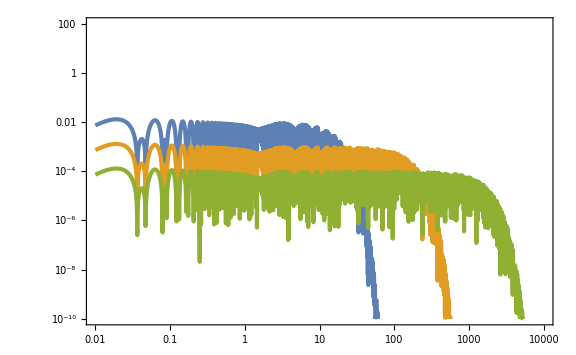

```mathematica
LogLogPlot[{Abs[CompactGintegrand[xp,10^1,5,6 10^-1,Sqrt[1/2]]],Abs[CompactGintegrand[xp,10^2,5,6 10^-1,Sqrt[1/2]]],Abs[CompactGintegrand[xp,10^3,5,6 10^-1,Sqrt[1/2]]]},{xp,10^-2,10^4},WorkingPrecision->30,PlotRange->{10^-10,10^2}]
```

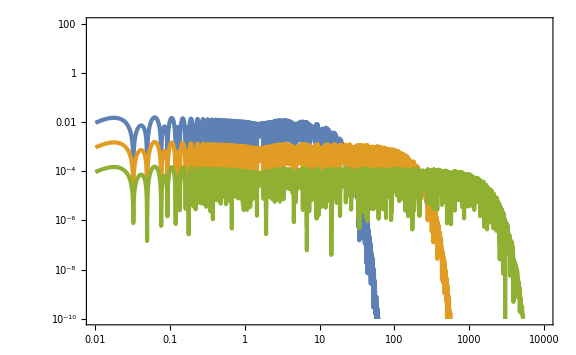

```mathematica
LogLogPlot[{Abs[CompactGintegrand[xp,10^1,5,6 10^-1,Sqrt[2/3]]],Abs[CompactGintegrand[xp,10^2,5,6 10^-1,Sqrt[2/3]]],Abs[CompactGintegrand[xp,10^3,5,6 10^-1,Sqrt[2/3]]]},{xp,10^-2,10^4},WorkingPrecision->30,PlotRange->{10^-10,10^2}]
```

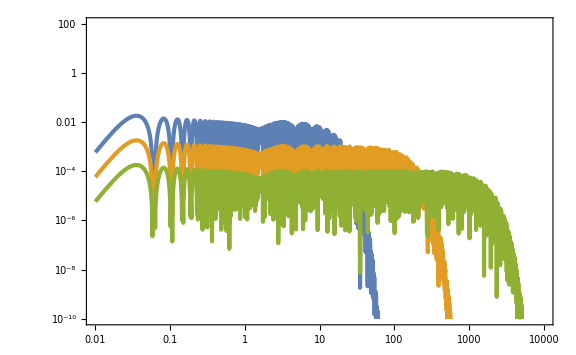

```mathematica
LogLogPlot[{Abs[CompactGintegrand[xp,10^1,5,6 10^-1,0]],Abs[CompactGintegrand[xp,10^2,5,6 10^-1,0]],Abs[CompactGintegrand[xp,10^3,5,6 10^-1,0]]},{xp,10^-2,10^4},WorkingPrecision->30,PlotRange->{10^-10,10^2}]
```

```mathematica
CompactG[x_,Nw_,mu_,kappa_]:=4π NIntegrate[deltax[xp,Nw,mu,kappa] Rx[xp,Nw,mu,kappa]^2 Rxp[xp,Nw,mu,kappa]Exp[(-Rx[xp,Nw,mu,kappa]^2)/(2 Rx[x,Nw,mu,kappa]^2)],{xp,0,10^1},WorkingPrecision->30,MaxRecursion->20]/(2Sqrt[2] π^(3/2)Rx[x,Nw,mu,kappa])
```

```mathematica
CompactG[10^1,5,2 10^-2,10]
```

0.00178948026600886988369385014291

```mathematica
<<init`
```

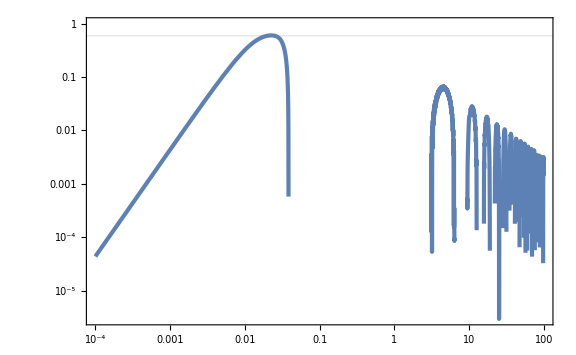

```mathematica
LogLogPlot[CompactRTH[x,5,2 10^-4,10^2],{x,10^-4,10^2},GridLines->{None,{0.59}}]
```

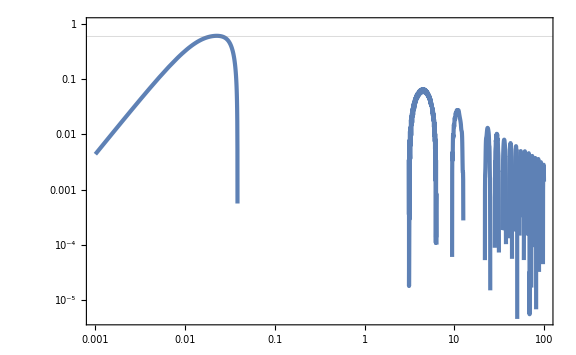

```mathematica
LogLogPlot[CompactRTH[x,5,0.02,10],{x,10^-3,10^2},GridLines->{None,{0.59}}]
```

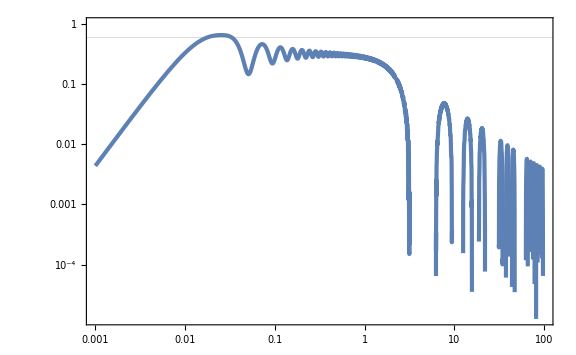

```mathematica
LogLogPlot[CompactRTH[x,5,2,1],{x,10^-3,10^2},GridLines->{None,{0.59}}]
```

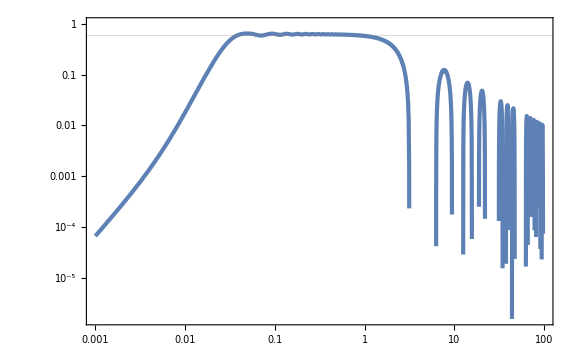

```mathematica
LogLogPlot[CompactRTH[x,5,3,0.1],{x,10^-3,10^2},GridLines->{None,{0.59}}]
```

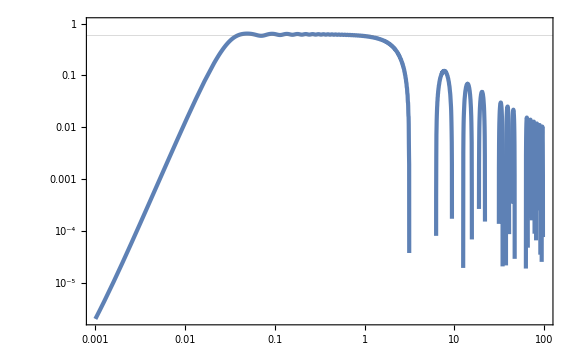

```mathematica
LogLogPlot[CompactRTH[x,5,3,0.01],{x,10^-3,10^2},GridLines->{None,{0.59}}]
```

```mathematica
CompactGList10=ParallelTable[{10^logx,CompactG[10^logx,5,3 10^-2,10]},{logx,-3,2,10^-1}];//AbsoluteTiming
```

{686.729,Null}

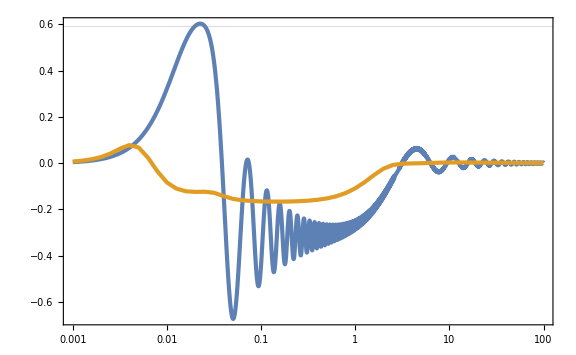

```mathematica
Show[LogLinearPlot[CompactRTH[x,5,2 10^-2,10],{x,10^-3,10^2},GridLines->{None,{0.59}}],ListLogLinearPlot[CompactGList10,PlotStyle->{Color[2],AbsoluteThickness[3]}]]
```

```mathematica
CompactGList001=Table[{10^logx,CompactG[10^logx,5,3,10^-2]},{logx,-3,2,10^-1}];//AbsoluteTiming
```

{1469.51,Null}

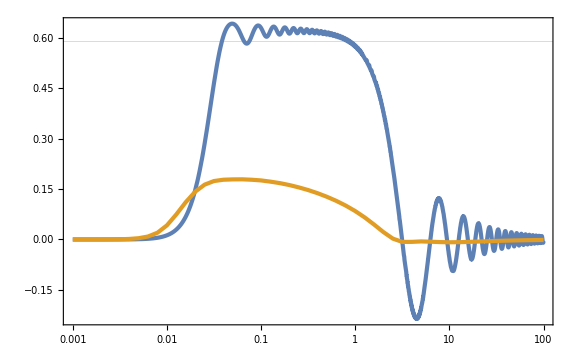

```mathematica
Show[LogLinearPlot[CompactRTH[x,5,3,10^-2],{x,10^-3,10^2},GridLines->{None,{0.59}}],ListLogLinearPlot[CompactGList001,PlotStyle->{Color[2],AbsoluteThickness[3]}]]
```